## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="FBP1";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
(*Q10 = 2.5; Average factor for biological systems*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "fit_FBP1";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(fdp^c+h2o^c→f6p^c+pi^c)^FBP1

Null; Null

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 41.5 | 39.425
43.575 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.0000154 | 0.0000134
0.0000174 |  | M | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004
1 | mg2 | 0.00062 | 0.000589
0.000651 | fdp | 0.0000175 | M | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | amp | 2.7×10^-6 | 2.565×10^-6
2.835×10^-6 | fdp | 0.0000175 | M | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 14.6 | 13.8
15.4 | 1/s | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004
1 | fdp | Null
pep | 0.002 | 43.8 | 41.61
45.99 | 1/s | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004
1 | fdp | Null
pep | 0.00004 | 21.9 | 20.805
22.995 | 1/s | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004
1 | fdp | Null
amp | 0.00001 | 7.3 | 6.935
7.665 | 1/s | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | f26bp | 3.×10^-7 | 2.85×10^-7
3.15×10^-7 | fdp | 0.0000175 | Competitive | fdp | 0.0000154 | M | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | amp | 1.1 | 1.045
1.155 |  |  | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0};
s05Priorities = {0};
kcatPriorities = {1,1,1,1};
inhibitionPriorities={0};
activationPriorities = Null;
otherParamsPriorities ={0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c+h2o^c→f6p^c+pi^c)^FBP1

Null; Null

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 41.5 | 39.425
43.575 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.0000154 | 0.0000134
0.0000174 |  | M | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 14.6 | 13.8
15.4 | 1/s | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004
1 | fdp | Null
pep | 0.002 | 43.8 | 41.61
45.99 | 1/s | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004
1 | fdp | Null
pep | 0.00004 | 21.9 | 20.805
22.995 | 1/s | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004
1 | fdp | Null
amp | 0.00001 | 7.3 | 6.935
7.665 | 1/s | 7.5 | 30 | trishcl | 0.1 | mg2 | 0.002
cl | 0.004

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_FBP1[c] + fdp[c] <=> E_FBP1[c]&fdp",
				"E_FBP1[c]&fdp <=> E_FBP1[c]&f6p&pi",
				"E_FBP1[c]&f6p&pi <=> E_FBP1[c]&f6p + pi[c]",
				"E_FBP1[c]&f6p <=> E_FBP1[c] + f6p[c]",
				
				"E_FBP1[c] + pep[c] <=> E_FBP1[c]&pep",
				"E_FBP1[c]&pep + fdp[c] <=> E_FBP1[c]&pep&fdp",
				"E_FBP1[c]&pep&fdp <=> E_FBP1[c]&pep&f6p&pi",
				"E_FBP1[c]&pep&f6p&pi <=> E_FBP1[c]&pep&f6p + pi[c]",
				"E_FBP1[c]&pep&f6p <=> E_FBP1[c]&pep + f6p[c]",

				"E_FBP1[c] + amp[c] <=> E_FBP1[c]&amp",
				"E_FBP1[c]&amp + fdp[c] <=> E_FBP1[c]&amp&fdp",
				"E_FBP1[c]&amp&fdp <=> E_FBP1[c]&amp&f6p&pi",
				"E_FBP1[c]&amp&f6p&pi <=> E_FBP1[c]&amp&f6p + pi[c]",
				"E_FBP1[c]&amp&f6p <=> E_FBP1[c]&amp + f6p[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{(*m["amp","c"], m["pep","c"]*)},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
```

```mathematica
enzymeModel["Reactions"]
```

{((FBP1^c)_^+amp^c⇌(FBP1^c&amp^c)_^)^FBP11,((FBP1^c)_^+pep^c⇌(FBP1^c&pep^c)_^)^FBP12,((FBP1^c)_^+fdp^c⇌(FBP1^c&fdp^c)_^)^FBP13,((FBP1^c&amp^c)_^+fdp^c⇌(FBP1^c&amp^c&fdp^c)_^)^FBP14,((FBP1^c&pep^c)_^+fdp^c⇌(FBP1^c&pep^c&fdp^c)_^)^FBP15,((FBP1^c&f6p^c)_^⇌(FBP1^c)_^+f6p^c)^FBP16,((FBP1^c&fdp^c)_^⇌(FBP1^c&f6p^c&pi^c)_^)^FBP17,((FBP1^c&amp^c&f6p^c)_^⇌(FBP1^c&amp^c)_^+f6p^c)^FBP18,((FBP1^c&amp^c&fdp^c)_^⇌(FBP1^c&amp^c&f6p^c&pi^c)_^)^FBP19,((FBP1^c&pep^c&f6p^c)_^⇌(FBP1^c&pep^c)_^+f6p^c)^FBP110,((FBP1^c&pep^c&fdp^c)_^⇌(FBP1^c&pep^c&f6p^c&pi^c)_^)^FBP111,((FBP1^c&f6p^c&pi^c)_^⇌(FBP1^c&f6p^c)_^+pi^c)^FBP112,((FBP1^c&amp^c&f6p^c&pi^c)_^⇌(FBP1^c&amp^c&f6p^c)_^+pi^c)^FBP113,((FBP1^c&pep^c&f6p^c&pi^c)_^⇌(FBP1^c&pep^c&f6p^c)_^+pi^c)^FBP114}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((FBP1^c)_^+fdp^c⇌(FBP1^c&fdp^c)_^)^FBP13,Overscript[(FBP1^c&f6p^c)_^⇌(FBP1^c)_^+f6p^c, FBP16],((FBP1^c&fdp^c)_^⇌(FBP1^c&f6p^c&pi^c)_^)^FBP17,Overscript[(FBP1^c&f6p^c&pi^c)_^⇌(FBP1^c&f6p^c)_^+pi^c, FBP112]};
catalyticReactionsSet2={((FBP1^c&pep^c)_^+fdp^c⇌(FBP1^c&pep^c&fdp^c)_^)^FBP15,Overscript[(FBP1^c&pep^c&f6p^c)_^⇌(FBP1^c&pep^c)_^+f6p^c, FBP110],((FBP1^c&pep^c&fdp^c)_^⇌(FBP1^c&pep^c&f6p^c&pi^c)_^)^FBP111,Overscript[(FBP1^c&pep^c&f6p^c&pi^c)_^⇌(FBP1^c&pep^c&f6p^c)_^+pi^c, FBP114]};
catalyticReactionsSet3={ ((FBP1^c&amp^c)_^+fdp^c⇌(FBP1^c&amp^c&fdp^c)_^)^FBP14,Overscript[(FBP1^c&amp^c&f6p^c)_^⇌(FBP1^c&amp^c)_^+f6p^c, FBP18],((FBP1^c&amp^c&fdp^c)_^⇌(FBP1^c&amp^c&f6p^c&pi^c)_^)^FBP19,Overscript[(FBP1^c&amp^c&f6p^c&pi^c)_^⇌(FBP1^c&amp^c&f6p^c)_^+pi^c, FBP113]};
(*catalyticReactionsSet1={((FBP1^c)_^+fdp^c⇌(FBP1^c&fdp^c)_^)^FBP12,((FBP1^c&f6p^c)_^⇌(FBP1^c)_^+f6p^c)^FBP14,((FBP1^c&fdp^c)_^⇌(FBP1^c&f6p^c&pi^c)_^)^FBP15,((FBP1^c&f6p^c&pi^c)_^⇌(FBP1^c&f6p^c)_^+pi^c)^FBP18};
catalyticReactionsSet2={((FBP1^c&pep^c)_^+fdp^c⇌(FBP1^c&pep^c&fdp^c)_^)^FBP13,((FBP1^c&pep^c&f6p^c)_^⇌(FBP1^c&pep^c)_^+f6p^c)^FBP16,((FBP1^c&pep^c&fdp^c)_^⇌(FBP1^c&pep^c&f6p^c&pi^c)_^)^FBP17,((FBP1^c&pep^c&f6p^c&pi^c)_^⇌(FBP1^c&pep^c&f6p^c)_^+pi^c)^FBP19};*)
catalyticReactionsSetsList = {catalyticReactionsSet1,catalyticReactionsSet2,catalyticReactionsSet3};
```

## Set up rate equations

```mathematica
deleteDirectoryContents[inputPath];
```

```mathematica
Get["MASSef`"];
```

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{fdp^c→0}

{f6p^c→0,pi^c→0}

{fdp^c→∞}

{f6p^c→∞,pi^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((FBP1^c&fdp^c)_^-((FBP1^c&f6p^c&pi^c)_^)/K_FBP17) Volume_c k_FBP17^⟶,((FBP1^c&amp^c&fdp^c)_^-((FBP1^c&amp^c&f6p^c&pi^c)_^)/K_FBP19) Volume_c k_FBP19^⟶,((FBP1^c&pep^c&fdp^c)_^-((FBP1^c&pep^c&f6p^c&pi^c)_^)/K_FBP111) Volume_c k_FBP111^⟶}

Volume_c (-(FBP1^c&pep^c&f6p^c&pi^c)_^ k_FBP111^⟵+(FBP1^c&pep^c&fdp^c)_^ k_FBP111^⟶-(FBP1^c&f6p^c&pi^c)_^ k_FBP17^⟵+(FBP1^c&fdp^c)_^ k_FBP17^⟶-(FBP1^c&amp^c&f6p^c&pi^c)_^ k_FBP19^⟵+(FBP1^c&amp^c&fdp^c)_^ k_FBP19^⟶)

1

2

3

38.681019

4

0.06391

5

0.006403

6

0.03159

Generating absolute rate forward equation...

Simplifying...

7.516574

Generating absolute rate reverse equation...

Simplifying...

21.12072

Generating relative rate forward equation...

Simplifying...

4.320982

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

35.904576

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	f6p[c]	fdp[c]	pep[c]	pi[c]	amp[c]	param_FBP1_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/haldaneRatio_3.txt"	41.5
1	0	1.5400000000000018e-6	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/relRateFor_fdp.txt"	0.090909090909091
1	0	2.4407355163901182e-6	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/relRateFor_fdp.txt"	0.13680688860321016
1	0	3.86830510452476e-6	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/relRateFor_fdp.txt"	0.20076000891310206
1	0	6.130850426523859e-6	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/relRateFor_fdp.txt"	0.2847472489508014
1	0	9.716743104994983e-6	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/relRateFor_fdp.txt"	0.3868631798468571
1	0	0.000015400000000000015	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/relRateFor_fdp.txt"	0.5000000000000002
1	0	0.000024407355163901183	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/relRateFor_fdp.txt"	0.6131368201531434
1	0	0.00003868305104524761	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/relRateFor_fdp.txt"	0.7152527510491989
1	0	0.00006130850426523859	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/relRateFor_fdp.txt"	0.7992399910868981
1	0	0.00009716743104994983	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/relRateFor_fdp.txt"	0.8631931113967902
1	0	0.00015400000000000017	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/relRateFor_fdp.txt"	0.9090909090909093
1	0	0.01	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	14.6
1	0	0.01	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	14.6
1	0	0.01	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	14.6
1	0	0.01	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	14.6
1	0	0.01	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	14.6
1	0	0.01	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	14.6
1	0	0.01	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	14.6
1	0	0.01	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	14.6
1	0	0.01	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	14.6
1	0	0.01	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	14.6
1	0	0.01	0	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	14.6
1	0	0.01	0.002	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	43.8
1	0	0.01	0.002	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	43.8
1	0	0.01	0.002	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	43.8
1	0	0.01	0.002	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	43.8
1	0	0.01	0.002	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	43.8
1	0	0.01	0.002	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	43.8
1	0	0.01	0.002	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	43.8
1	0	0.01	0.002	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	43.8
1	0	0.01	0.002	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	43.8
1	0	0.01	0.002	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	43.8
1	0	0.01	0.002	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	43.8
1	0	0.01	0.00004	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	21.9
1	0	0.01	0.00004	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	21.9
1	0	0.01	0.00004	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	21.9
1	0	0.01	0.00004	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	21.9
1	0	0.01	0.00004	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	21.9
1	0	0.01	0.00004	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	21.9
1	0	0.01	0.00004	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	21.9
1	0	0.01	0.00004	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	21.9
1	0	0.01	0.00004	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	21.9
1	0	0.01	0.00004	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	21.9
1	0	0.01	0.00004	0	0	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	21.9
1	0	0.01	0	0	0.00001	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	7.3
1	0	0.01	0	0	0.00001	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	7.3
1	0	0.01	0	0	0.00001	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	7.3
1	0	0.01	0	0	0.00001	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	7.3
1	0	0.01	0	0	0.00001	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	7.3
1	0	0.01	0	0	0.00001	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	7.3
1	0	0.01	0	0	0.00001	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	7.3
1	0	0.01	0	0	0.00001	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	7.3
1	0	0.01	0	0	0.00001	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	7.3
1	0	0.01	0	0	0.00001	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	7.3
1	0	0.01	0	0	0.00001	1	7.5	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme1/fit_FBP1/input/absRateFor.txt"	7.3

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 3.50142005646
best_fit: 3.50111999099
best_fit: 3.50153620143
best_fit: 3.55204618847
best_fit: 3.50531817105
best_fit: 1.28350308747
best_fit: 1.28198955769
best_fit: 3.5009272882
best_fit: 1.28122092464
best_fit: 3.50090294072
best_fit: 4.2256127293
best_fit: 1.33880434223
best_fit: 3.50103804707
best_fit: 3.50092776213
best_fit: 3.50099054765
best_fit: 3.50095730272
best_fit: 1.0183106341
best_fit: 1.3893657497
best_fit: 3.50110437108
best_fit: 3.50234699641
best_fit: 3.50328232034
best_fit: 4.20904362755
best_fit: 3.50808788442
best_fit: 1.28146967517
best_fit: 1.28469314691
best_fit: 1.30293397514
best_fit: 3.50583726598
best_fit: 3.50133195045
best_fit: 3.50149289151
best_fit: 6.36615469225
best_fit: 1.30435861366
best_fit: 3.5093166501
best_fit: 3.50097675987
best_fit: 3.50103848174
best_fit: 4.18083888032
best_fit: 3.50119919929
best_fit: 1.28590916917
best_fit: 3.50156224508
best_fit: 3.50100368579
best_fit: 3.50092035265
best_fit: 1.29587081813
best_fit: 3.5011187635
best_fit: 1.28100119405
best_fit: 1.29716139086
best_fit: 1.28189328441
best_fit: 1.29272968866
best_fit: 3.50109069667
best_fit: 3.50111202915
best_fit: 4.2084261814
best_fit: 1.37530310705
best_fit: 3.5013482011
best_fit: 3.50106520211
best_fit: 1.87138495478
best_fit: 1.33229114891
best_fit: 3.50091035833
best_fit: 6.41501621554
best_fit: 3.53846852331
best_fit: 3.50139293404
best_fit: 0.823654477085
best_fit: 1.28970305149
best_fit: 1.09970807006
best_fit: 3.5034119621
best_fit: 1.09633815888
best_fit: 3.50209902687
best_fit: 1.34350014562
best_fit: 3.50111745386
best_fit: 1.28453605159
best_fit: 1.36602570496
best_fit: 1.32255413659
best_fit: 1.39857062054
best_fit: 3.50583858416
best_fit: 3.55572180192
best_fit: 3.50145912771
best_fit: 3.50095727672
best_fit: 3.50158553267
best_fit: 3.50090220013
best_fit: 3.5009900963
best_fit: 1.29759120476
best_fit: 1.31489189308
best_fit: 3.50079981512
best_fit: 3.50157677477
best_fit: 1.28476633183
best_fit: 3.50388543499
best_fit: 3.50091421293
best_fit: 1.28763038567
best_fit: 1.28391670188
best_fit: 1.35064120694
best_fit: 3.50096803958
best_fit: 3.50144133493
best_fit: 3.50102402019
best_fit: 3.50097690364
best_fit: 1.28084511442
best_fit: 1.2886300261
best_fit: 11.9727382396
best_fit: 3.5010738857
best_fit: 3.50089493413
best_fit: 1.29196492817
best_fit: 1.38102507969
best_fit: 1.28279057241
best_fit: 1.29500876092

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.20914×10^-11 | 1.46203×10^-22 | 1.15543×10^-9 | 2.78418×10^-9 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.20914×10^-11 | 1.46203×10^-22 | 1.15543×10^-9 | 2.78418×10^-9 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.20914×10^-11 | 1.46203×10^-22 | 1.15543×10^-9 | 2.78418×10^-9 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.20914×10^-11 | 1.46203×10^-22 | 1.15543×10^-9 | 2.78418×10^-9 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.20914×10^-11 | 1.46203×10^-22 | 1.15543×10^-9 | 2.78418×10^-9 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.20914×10^-11 | 1.46203×10^-22 | 1.15543×10^-9 | 2.78418×10^-9 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.20914×10^-11 | 1.46203×10^-22 | 1.15543×10^-9 | 2.78418×10^-9 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.20914×10^-11 | 1.46203×10^-22 | 1.15543×10^-9 | 2.78418×10^-9 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.20914×10^-11 | 1.46203×10^-22 | 1.15543×10^-9 | 2.78418×10^-9 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.20914×10^-11 | 1.46203×10^-22 | 1.15543×10^-9 | 2.78418×10^-9 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.20914×10^-11 | 1.46203×10^-22 | 1.15543×10^-9 | 2.78418×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 7.90701×10^-12 | 6.25208×10^-23 | 7.55577×10^-10 | 1.82067×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 7.90701×10^-12 | 6.25208×10^-23 | 7.55577×10^-10 | 1.82067×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 7.90701×10^-12 | 6.25208×10^-23 | 7.55577×10^-10 | 1.82067×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 7.90701×10^-12 | 6.25208×10^-23 | 7.55577×10^-10 | 1.82067×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 7.90701×10^-12 | 6.25208×10^-23 | 7.55577×10^-10 | 1.82067×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 7.90701×10^-12 | 6.25208×10^-23 | 7.55577×10^-10 | 1.82067×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 7.90701×10^-12 | 6.25208×10^-23 | 7.55577×10^-10 | 1.82067×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 7.90701×10^-12 | 6.25208×10^-23 | 7.55577×10^-10 | 1.82067×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 7.90701×10^-12 | 6.25208×10^-23 | 7.55577×10^-10 | 1.82067×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 7.90701×10^-12 | 6.25208×10^-23 | 7.55577×10^-10 | 1.82067×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 7.90701×10^-12 | 6.25208×10^-23 | 7.55577×10^-10 | 1.82067×10^-9 | 41.5 | 41.5
1 | haldaneRatio_3 | 2.09366×10^-12 | 4.38341×10^-24 | 2.00068×10^-10 | 4.8209×10^-10 | 41.5 | 41.5
1 | haldaneRatio_3 | 2.09366×10^-12 | 4.38341×10^-24 | 2.00068×10^-10 | 4.8209×10^-10 | 41.5 | 41.5
1 | haldaneRatio_3 | 2.09366×10^-12 | 4.38341×10^-24 | 2.00068×10^-10 | 4.8209×10^-10 | 41.5 | 41.5
1 | haldaneRatio_3 | 2.09366×10^-12 | 4.38341×10^-24 | 2.00068×10^-10 | 4.8209×10^-10 | 41.5 | 41.5
1 | haldaneRatio_3 | 2.09366×10^-12 | 4.38341×10^-24 | 2.00068×10^-10 | 4.8209×10^-10 | 41.5 | 41.5
1 | haldaneRatio_3 | 2.09366×10^-12 | 4.38341×10^-24 | 2.00068×10^-10 | 4.8209×10^-10 | 41.5 | 41.5
1 | haldaneRatio_3 | 2.09366×10^-12 | 4.38341×10^-24 | 2.00068×10^-10 | 4.8209×10^-10 | 41.5 | 41.5
1 | haldaneRatio_3 | 2.09366×10^-12 | 4.38341×10^-24 | 2.00068×10^-10 | 4.8209×10^-10 | 41.5 | 41.5
1 | haldaneRatio_3 | 2.09366×10^-12 | 4.38341×10^-24 | 2.00068×10^-10 | 4.8209×10^-10 | 41.5 | 41.5
1 | haldaneRatio_3 | 2.09366×10^-12 | 4.38341×10^-24 | 2.00068×10^-10 | 4.8209×10^-10 | 41.5 | 41.5
1 | haldaneRatio_3 | 2.09366×10^-12 | 4.38341×10^-24 | 2.00068×10^-10 | 4.8209×10^-10 | 41.5 | 41.5
1 | relRateFor_fdp | 1.37645×10^-12 | 1.89463×10^-24 | 2.88158×10^-13 | 3.16974×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_fdp | 1.30707×10^-12 | 1.70842×10^-24 | 4.11754×10^-13 | 3.00975×10^-10 | 0.136807 | 0.136807
1 | relRateFor_fdp | 1.21025×10^-12 | 1.46472×10^-24 | 5.59441×10^-13 | 2.78662×10^-10 | 0.20076 | 0.20076
1 | relRateFor_fdp | 1.08291×10^-12 | 1.1727×10^-24 | 7.10043×10^-13 | 2.49359×10^-10 | 0.284747 | 0.284747
1 | relRateFor_fdp | 9.28424×10^-13 | 8.61971×10^-25 | 8.27005×10^-13 | 2.13772×10^-10 | 0.386863 | 0.386863
1 | relRateFor_fdp | 7.57283×10^-13 | 5.73478×10^-25 | 8.71803×10^-13 | 1.74361×10^-10 | 0.5 | 0.5
1 | relRateFor_fdp | 5.85837×10^-13 | 3.43205×10^-25 | 8.27116×10^-13 | 1.34899×10^-10 | 0.613137 | 0.613137
1 | relRateFor_fdp | 4.31155×10^-13 | 1.85895×10^-25 | 7.10099×10^-13 | 9.92794×10^-11 | 0.715253 | 0.715253
1 | relRateFor_fdp | 3.03937×10^-13 | 9.2378×10^-26 | 5.5933×10^-13 | 6.99828×10^-11 | 0.79924 | 0.79924
1 | relRateFor_fdp | 2.07279×10^-13 | 4.29644×10^-26 | 4.12004×10^-13 | 4.77302×10^-11 | 0.863193 | 0.863193
1 | relRateFor_fdp | 1.37744×10^-13 | 1.89734×10^-26 | 2.88325×10^-13 | 3.17157×10^-11 | 0.909091 | 0.909091
1 | absRateFor | 7.23865×10^-13 | 5.23981×10^-25 | 2.43308×10^-11 | 1.66649×10^-10 | 14.6 | 14.6
1 | absRateFor | 7.23865×10^-13 | 5.23981×10^-25 | 2.43308×10^-11 | 1.66649×10^-10 | 14.6 | 14.6
1 | absRateFor | 7.23865×10^-13 | 5.23981×10^-25 | 2.43308×10^-11 | 1.66649×10^-10 | 14.6 | 14.6
1 | absRateFor | 7.23865×10^-13 | 5.23981×10^-25 | 2.43308×10^-11 | 1.66649×10^-10 | 14.6 | 14.6
1 | absRateFor | 7.23865×10^-13 | 5.23981×10^-25 | 2.43308×10^-11 | 1.66649×10^-10 | 14.6 | 14.6
1 | absRateFor | 7.23865×10^-13 | 5.23981×10^-25 | 2.43308×10^-11 | 1.66649×10^-10 | 14.6 | 14.6
1 | absRateFor | 7.23865×10^-13 | 5.23981×10^-25 | 2.43308×10^-11 | 1.66649×10^-10 | 14.6 | 14.6
1 | absRateFor | 7.23865×10^-13 | 5.23981×10^-25 | 2.43308×10^-11 | 1.66649×10^-10 | 14.6 | 14.6
1 | absRateFor | 7.23865×10^-13 | 5.23981×10^-25 | 2.43308×10^-11 | 1.66649×10^-10 | 14.6 | 14.6
1 | absRateFor | 7.23865×10^-13 | 5.23981×10^-25 | 2.43308×10^-11 | 1.66649×10^-10 | 14.6 | 14.6
1 | absRateFor | 7.23865×10^-13 | 5.23981×10^-25 | 2.43308×10^-11 | 1.66649×10^-10 | 14.6 | 14.6
1 | absRateFor | 3.40572×10^-12 | 1.15989×10^-23 | 3.43483×10^-10 | 7.84209×10^-10 | 43.8 | 43.8
1 | absRateFor | 3.40572×10^-12 | 1.15989×10^-23 | 3.43483×10^-10 | 7.84209×10^-10 | 43.8 | 43.8
1 | absRateFor | 3.40572×10^-12 | 1.15989×10^-23 | 3.43483×10^-10 | 7.84209×10^-10 | 43.8 | 43.8
1 | absRateFor | 3.40572×10^-12 | 1.15989×10^-23 | 3.43483×10^-10 | 7.84209×10^-10 | 43.8 | 43.8
1 | absRateFor | 3.40572×10^-12 | 1.15989×10^-23 | 3.43483×10^-10 | 7.84209×10^-10 | 43.8 | 43.8
1 | absRateFor | 3.40572×10^-12 | 1.15989×10^-23 | 3.43483×10^-10 | 7.84209×10^-10 | 43.8 | 43.8
1 | absRateFor | 3.40572×10^-12 | 1.15989×10^-23 | 3.43483×10^-10 | 7.84209×10^-10 | 43.8 | 43.8
1 | absRateFor | 3.40572×10^-12 | 1.15989×10^-23 | 3.43483×10^-10 | 7.84209×10^-10 | 43.8 | 43.8
1 | absRateFor | 3.40572×10^-12 | 1.15989×10^-23 | 3.43483×10^-10 | 7.84209×10^-10 | 43.8 | 43.8
1 | absRateFor | 3.40572×10^-12 | 1.15989×10^-23 | 3.43483×10^-10 | 7.84209×10^-10 | 43.8 | 43.8
1 | absRateFor | 3.40572×10^-12 | 1.15989×10^-23 | 3.43483×10^-10 | 7.84209×10^-10 | 43.8 | 43.8
1 | absRateFor | 1.63713×10^-12 | 2.68021×10^-24 | 8.25509×10^-11 | 3.76945×10^-10 | 21.9 | 21.9
1 | absRateFor | 1.63713×10^-12 | 2.68021×10^-24 | 8.25509×10^-11 | 3.76945×10^-10 | 21.9 | 21.9
1 | absRateFor | 1.63713×10^-12 | 2.68021×10^-24 | 8.25509×10^-11 | 3.76945×10^-10 | 21.9 | 21.9
1 | absRateFor | 1.63713×10^-12 | 2.68021×10^-24 | 8.25509×10^-11 | 3.76945×10^-10 | 21.9 | 21.9
1 | absRateFor | 1.63713×10^-12 | 2.68021×10^-24 | 8.25509×10^-11 | 3.76945×10^-10 | 21.9 | 21.9
1 | absRateFor | 1.63713×10^-12 | 2.68021×10^-24 | 8.25509×10^-11 | 3.76945×10^-10 | 21.9 | 21.9
1 | absRateFor | 1.63713×10^-12 | 2.68021×10^-24 | 8.25509×10^-11 | 3.76945×10^-10 | 21.9 | 21.9
1 | absRateFor | 1.63713×10^-12 | 2.68021×10^-24 | 8.25509×10^-11 | 3.76945×10^-10 | 21.9 | 21.9
1 | absRateFor | 1.63713×10^-12 | 2.68021×10^-24 | 8.25509×10^-11 | 3.76945×10^-10 | 21.9 | 21.9
1 | absRateFor | 1.63713×10^-12 | 2.68021×10^-24 | 8.25509×10^-11 | 3.76945×10^-10 | 21.9 | 21.9
1 | absRateFor | 1.63713×10^-12 | 2.68021×10^-24 | 8.25509×10^-11 | 3.76945×10^-10 | 21.9 | 21.9
1 | absRateFor | 2.68574×10^-12 | 7.2132×10^-24 | 4.51443×10^-11 | 6.18416×10^-10 | 7.3 | 7.3
1 | absRateFor | 2.68574×10^-12 | 7.2132×10^-24 | 4.51443×10^-11 | 6.18416×10^-10 | 7.3 | 7.3
1 | absRateFor | 2.68574×10^-12 | 7.2132×10^-24 | 4.51443×10^-11 | 6.18416×10^-10 | 7.3 | 7.3
1 | absRateFor | 2.68574×10^-12 | 7.2132×10^-24 | 4.51443×10^-11 | 6.18416×10^-10 | 7.3 | 7.3
1 | absRateFor | 2.68574×10^-12 | 7.2132×10^-24 | 4.51443×10^-11 | 6.18416×10^-10 | 7.3 | 7.3
1 | absRateFor | 2.68574×10^-12 | 7.2132×10^-24 | 4.51443×10^-11 | 6.18416×10^-10 | 7.3 | 7.3
1 | absRateFor | 2.68574×10^-12 | 7.2132×10^-24 | 4.51443×10^-11 | 6.18416×10^-10 | 7.3 | 7.3
1 | absRateFor | 2.68574×10^-12 | 7.2132×10^-24 | 4.51443×10^-11 | 6.18416×10^-10 | 7.3 | 7.3
1 | absRateFor | 2.68574×10^-12 | 7.2132×10^-24 | 4.51443×10^-11 | 6.18416×10^-10 | 7.3 | 7.3
1 | absRateFor | 2.68574×10^-12 | 7.2132×10^-24 | 4.51443×10^-11 | 6.18416×10^-10 | 7.3 | 7.3
1 | absRateFor | 2.68574×10^-12 | 7.2132×10^-24 | 4.51443×10^-11 | 6.18416×10^-10 | 7.3 | 7.3

### Simulated Data and Best Fit Data Plot

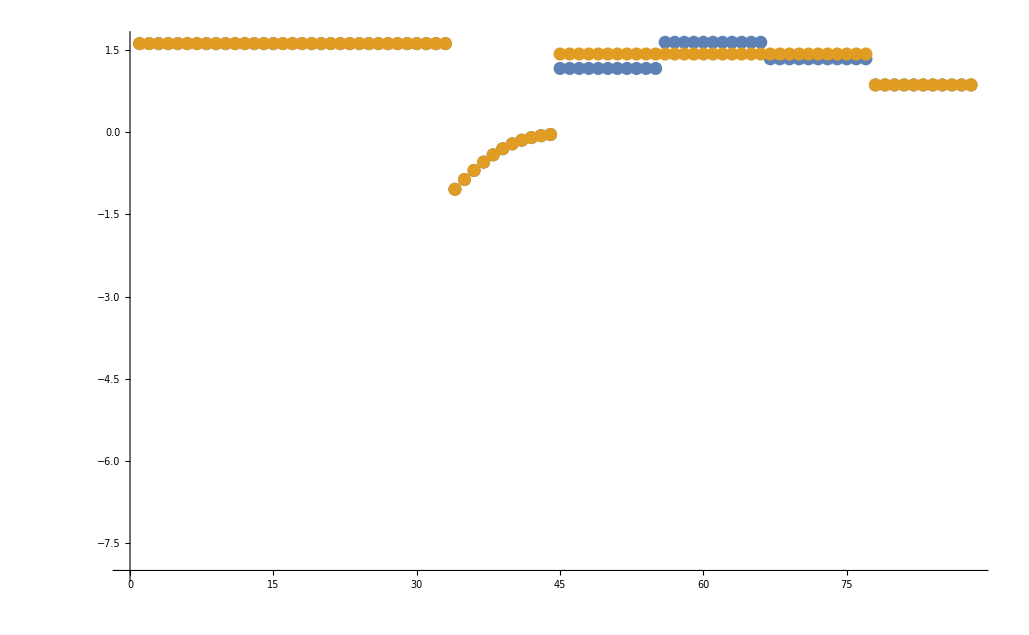

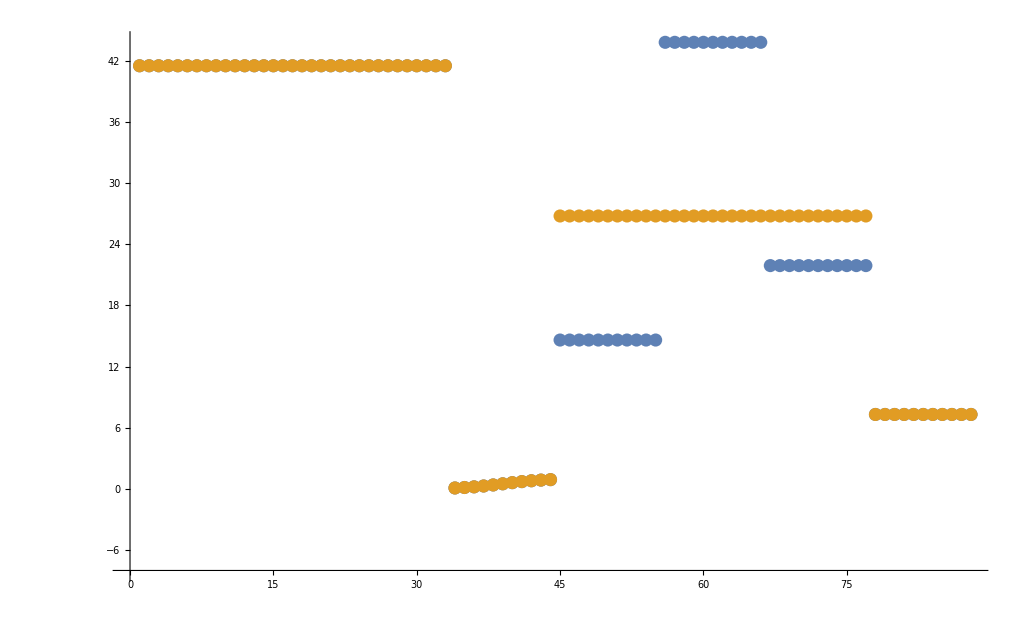

```mathematica
datasetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

```mathematica
2
```

```mathematica
amp a
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 2.51272×10^-6
0.00089 | 0.00089 | 1.39821×10^-6
0.00053 | 0.00053 | 1.35758×10^-6

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 3.33383×10^-6

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 8.29398×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 4.57492×10^-6